```mathematica
LagrangianEquations[T_,V_,Q_:0,genCoords_List]:=Module[{L=T-V},(D[D[L,D[#,t]],t]==Q+D[L,#])&/@genCoords]
```

{{0.1,0.2,0.03,15000.,6.,1.,,0.174533,0.174533,0.,0.,0.3,0.3,1.7,1.,6.},{0.12,0.19,0.03,15000.,6.,1.,,,,,,,,,,}}

6.

{{α[t]→InterpolatingFunction[…][t],β[t]→InterpolatingFunction[…][t]}}

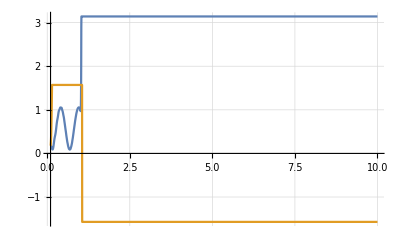

```mathematica
nm=2 ; (*Количество мышц*)
DataTable=Import["C:/Users/Warsars/Documents/Программирование и проекты/Расчетка Биомеханика/Data/muscles.xls",{"Data",1,Range[2,1+nm],Range[2,17]}] (*Импорт данных о мышцах, необходимо указать путь к файлу с данными*)

a=DataTable[[All,1]];
b=DataTable[[All,2]];
c=DataTable[[All,3]];
g=9.8;
k=DataTable[[All,4]];
A=DataTable[[All,5]];
B=DataTable[[All,6]];
Subscript[α, 0]=DataTable[[1,8]];
Subscript[β, 0]=DataTable[[1,9]];
Subscript[υ, α0]=DataTable[[1,10]];
Subscript[υ, β0]=DataTable[[1,11]];
Subscript[S, 1]=DataTable[[1,12]];
Subscript[S, 2]=DataTable[[1,13]];
Subscript[m, 1]=DataTable[[1,14]];
Subscript[m, 2]=DataTable[[1,15]];
Subscript[m, gr]=DataTable[[1,16]]
(*Доп углы*)
γ=(π/2+β[t])/2;(*Угол связки в локте*)
(*Скорости*)
Subscript[ω, 1]=D[α[t],t];
Subscript[ω, 2]=D[β[t],t];
(*Расчет Лагранжа*)
Subscript[i, 1]=Subscript[m, 1] Subscript[S, 1]^2/3;
Subscript[i, 2]=Subscript[m, 2] Subscript[S, 2]^2/3;
Subscript[l, 1]=a^2+c^2+2a*c Cos[γ];
Subscript[l, 2]=b^2+c^2+2b*c Cos[γ];
Δx=Range[1,nm];
For[i=1,i<3,i++,Δx[[i]]=((Subscript[l, 1][[i]]+Subscript[l, 2][[i]])-(Subscript[l, 1][[i]]/.γ->π/2+Subscript[l, 2][[i]]/.γ->π/2))];

κ=Subscript[i, 1] Subscript[ω, 1]^2/2 + Subscript[i, 2] Subscript[ω, 2]^2/2+(Subscript[ω, 1] Subscript[S, 1])^2 Subscript[m, 2]/2;
Πk=Sum[k[[i]]*(Δx[[i]])^2/2,{i,1,nm}];

(*Π=Πk+(Subscript[S, 1]+Subscript[S, 2]-Subscript[S, 1]/2 Cos[α[t]])Subscript[m, 1] g+(Subscript[S, 1]+Subscript[S, 2]-Subscript[S, 1] Cos[α[t]]-Subscript[S, 2]/2 Sin[β[t]-α[t]])Subscript[m, 2] g+(Subscript[S, 1]+Subscript[S, 2]-Subscript[S, 1] Cos[α[t]]-Subscript[S, 2] Sin[β[t]-α[t]])Subscript[m, gr] g;*) (*Потециальная энергия версия 1*)
Π=Πk+(-Subscript[S, 1]/2 Cos[α[t]])Subscript[m, 1] g+(-Subscript[S, 1]Cos[α[t]]+Subscript[S, 2]/2 Cos[β[t]+π/2-α[t]])Subscript[m, 2] g+(-Subscript[S, 1]Cos[α[t]]+Subscript[S, 2] Cos[β[t]+π/2-α[t]])Subscript[m, gr] g;
υ=D[Subscript[l, 1]+Subscript[l, 2],t];
Subscript[F, d]=-Sum[B[[i]]*υ[[i]],{i,1,nm}];
Q=Subscript[F, d]+Sum[A[[i]],{i,1,nm}];
eqs=LagrangianEquations[κ,Π,Q,{α[t],β[t]}];
IC={α[0.1]==Subscript[α, 0],β[0.1]==Subscript[β, 0],α'[0.1]==Subscript[υ, α0],β'[0.1]==Subscript[υ, β0]};
sol=NDSolve[Join[eqs,IC],{α[t],β[t]},{t,0.1,1}]
fβ[t]= β[t]/.sol;
fα[t]= α[t]/.sol;
Plot[{Clip[fα[t],{0,π}],Clip[fβ[t],{-π/2,π/2}]},{t,0.1,10},GridLines->Automatic]
```